```mathematica
5+5
```

10

```mathematica
Clear[throttle]
ro=1.225
Dia=0.25
Co=0.015
R=10000
f=3.2
P=Co*((throttle*R/1000)^f)
T=((Pi/2)*0.25^2*1.225*P^2)^(1/3)*8-9.80665
```

1.225

0.25

0.015

10000

3.2

23.7734 throttle^3.2

-9.80665+32.6485 (throttle^6.4)^(1/3)

```mathematica
x=6.876
```

6.876

```mathematica
(0.027100266680146246+0.0082903743929312x+0.0008453829180128993 x^2+0.000028735022255744805 x^3)^0.15625
```

0.729984

```mathematica
NSolve[-9.80665+32.64846901558475(t^6.4)^(1/3)==x,t]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{t→1. (0.0271003+0.00829037 x+0.000845383 x^2+0.000028735 x^3)^0.15625}}

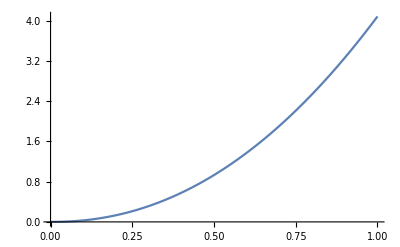

```mathematica
Plot[4.081058626948094 (t^6.4)^(1/3),{t,0,1}]
```

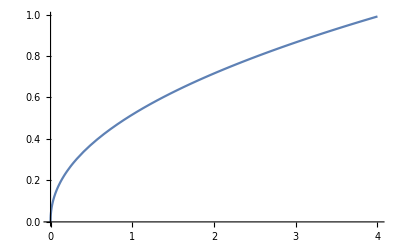

```mathematica
Plot[0.5172496842054825 (x^3)^0.15625,{x,0,4}]
```

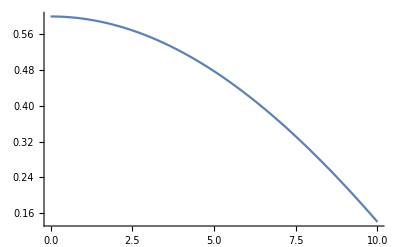

```mathematica
Plot[Cos[x/10]-0.4,{x,0,10}]
```

```mathematica
6.876*1
```

6.876

```mathematica
6.876/2
```

3.438

```mathematica
13.276/2
```

6.638

```mathematica
35.58004-9.81*3
```

6.15004